Definition of RK4

```mathematica
crkamat={{1/2},{0,1/2},{0,0,1}};
crkbvec={1/6,1/3,1/3,1/6};
crkcvec={1/2,1/2,1};
ClassicalRungeKuttaCoefficients[4,p_]:=N[{crkamat,crkbvec,crkcvec},p];
```

Compile the NDSolve parameter sweep

```mathematica
events=Compile[
{{pList,_Real,1},{τList,_Real,1}},
res=Table[
counter1=0;
NDSolve[
{
v'[t] ==-9.81,
x'[t] ==v[t]-p[[i]]*v[t-τ[[j]]],
x[t/;t≤0] ==20,
v[t/;t≤0] ==0,
WhenEvent[x[t]==0,v[t]-> -0.95 * v[t],"DetectionMethod"->"Sign"],
WhenEvent[x[t]==0,counter1 = counter1+1,"DetectionMethod"->"Sign"]
},
{x[t],v[t]},
{t,0,60},
InterpolationOrder->All,
Method->{"ExplicitRungeKutta","DifferenceOrder"->4,"Coefficients"->ClassicalRungeKuttaCoefficients},
StartingStepSize->N@60/10000,
MaxSteps->11100
];
{pList[[i]],τList[[j]],counter1},
{i,Length@pList},{j,Length@τList}];
res=Transpose[Flatten@res[[All,All,#]]&/@Range[3]],
CompilationTarget->"C",
"RuntimeOptions"->"Speed"
]
```

CompiledFunction[…]

Run and Benchmark

```mathematica
n=32;
pLen = n;
p =N@ Range[0.1,1.5,1.4/(pLen-1)];
τLen = n;
τ =N@ Range[0.1,2,1.9/(pLen-1)];
runtime=Timing[endvals=events[p,τ]];
runtime[[1]]
```

304.859

Plot endvals

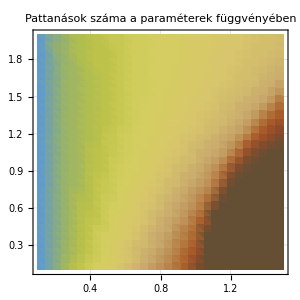

events_endvals.png

```mathematica
plt=ListDensityPlot[
endvals[[All,{1,2,3}]],
PlotLegends->Placed[Automatic,Below],
FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"p","\\tau"},
ImageSize->300,
ColorFunction->"SouthwestColors",
InterpolationOrder->1,
PlotLabel->Style["Pattanások száma a paraméterek függvényében",14,Black]
]
Export["events_endvals.png",plt,ImageResolution->700]
```